```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nTrajectory=input[[6]];
nstore=input[[8]];
yWall=input[[10]];
sigmaXX=input[[12]];
sigmaXZ=input[[14]];
transitTime=input[[16]];
sigmaPX=input[[18]];
sigmaPY=input[[20]];
sigmaPZ=input[[22]];
density=input[[24]];
rabi=input[[26]];
kappa=input[[28]];
name =input[[30]]
```

tau1_dens50_g2_k40

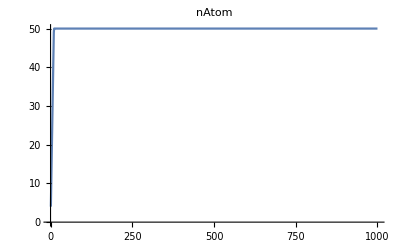

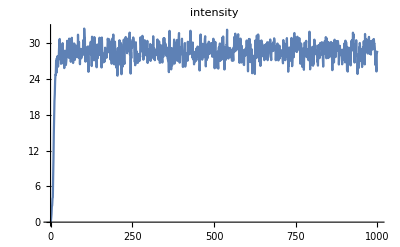

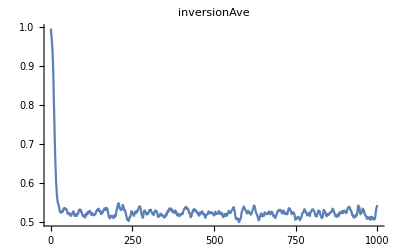

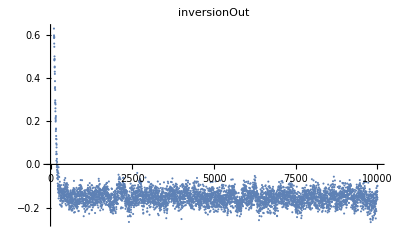

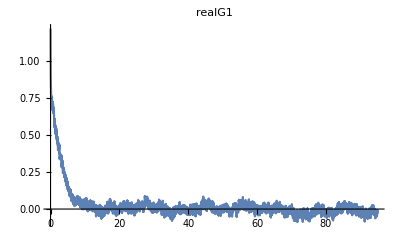

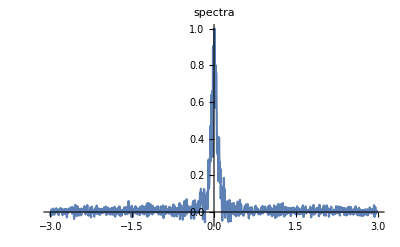

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

FittedModel[0.00238868/(0.00292786+x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.108219 | 0.00205255 | 52.7244 | 8.88028839826×10^-308
A | 0.0441452 | 0.000592048 | 74.5636 | 2.54874023353×10^-440

0.108219

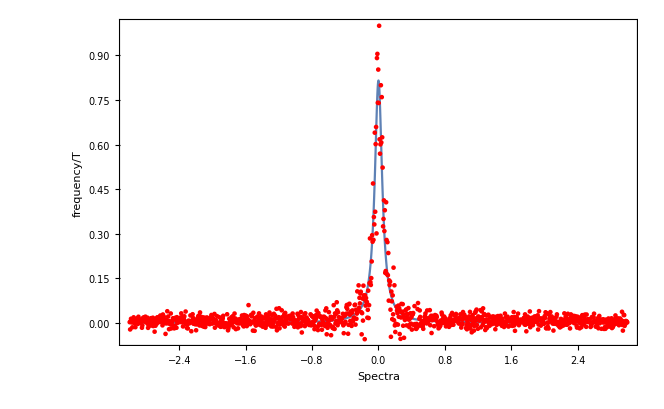

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A(1/2 linewidth)/(x^2+(1/2 linewidth)^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-3,3},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.005],Map[Point,spectra]}]},Frame->True,FrameLabel->{"Spectra","frequency/T"}]
```

B ⅇ^(-t/tc)

FittedModel[0.881594 ⅇ^(-0.3405 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 2.93686 | 0.0143551 | 204.587 | 1.082831524×10^-3483
B | 0.881594 | 0.00304184 | 289.822 | 1.3724049059×10^-4719

2.93686

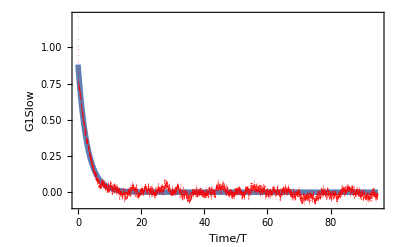

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tc=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth form the coherent time*)
linewidth2 = 1/(tc Pi)
```

0.108385

```mathematica
(*Notice there is another exponential decay.*)
```

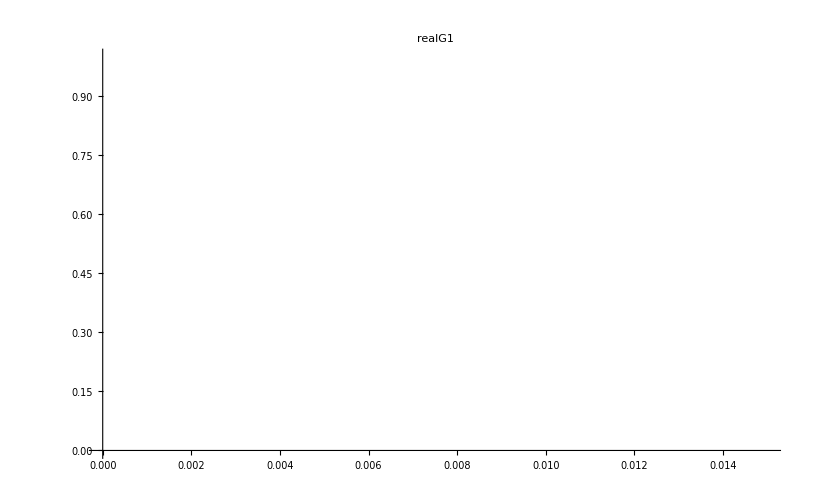

B2 ⅇ^(-d π t)

FittedModel[1.21619 ⅇ^(-3.14159 t)]

FittedModel::dof: The number of parameters 2 is not less than the number of data values 1. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

Missing[]

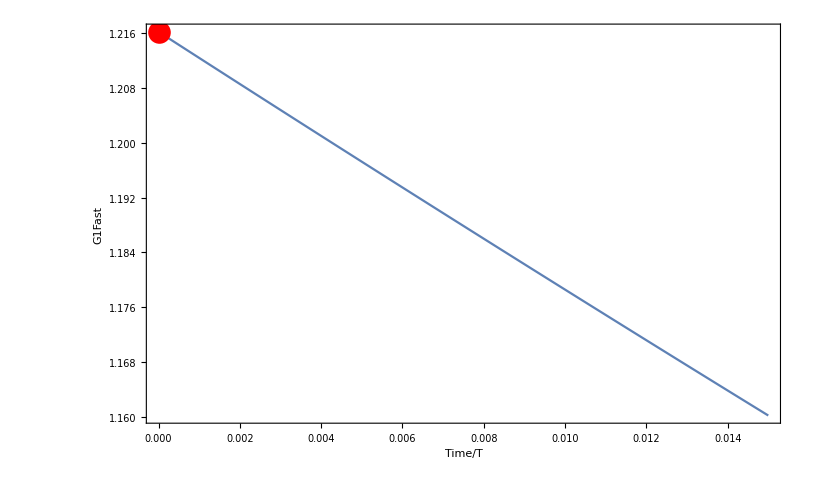

```mathematica
cutOff = 0.015;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,1}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- d Pi t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{d,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(d Pi)/.fitExp2["BestFitParameters"]
```

0.31831